```mathematica
PointsGA = {{0.10, 0.20},{0.10,0.30},{0.1,0.40},{0.50,0.20},{0.50,0.30},{0.50,0.40},{0.90,0.20},{0.90,0.30},{0.90,0.40}};
```

```mathematica
ValueG60 = {};
For[i=1,i≤ Length[PointsGA],i++,
ValueG60 = Insert[ValueG60,BEMG[PointsGA[[i,1]],PointsGA[[i,2]]],-1]
]
ValueG60
```

{0.253793,0.374455,0.488432,0.326824,0.469954,0.595719,0.772824,0.895567,0.976611}

```mathematica
ValueG120 = {};
For[i=1,i≤ Length[PointsGA],i++,
ValueG120 = Insert[ValueG120,BEMG[PointsGA[[i,1]],PointsGA[[i,2]]],-1]
]
ValueG120
```

{0.253729,0.374364,0.488321,0.326673,0.469769,0.595523,0.771899,0.895035,0.976256}

```mathematica
PointsGA2 = {{0.10,0.95},{0.10,0.96},{0.10,0.97},{0.10,0.98},{0.10,0.99}}
```

{{0.1,0.95},{0.1,0.96},{0.1,0.97},{0.1,0.98},{0.1,0.99}}

```mathematica
ValueG802={};
For[i=1,i≤ Length[PointsGA2],i++,
ValueG802 = Insert[ValueG802,BEMG[PointsGA2[[i,1]],PointsGA2[[i,2]]],-1]
]
ValueG802
```

{0.970807,0.977434,0.983995,0.990492,0.99693}

```mathematica
ValueG802 - ValueExact2
```

{0.000104368,0.000104222,0.000104274,0.000105507,0.000112669}

```mathematica
ValueG1203={};
For[i=1,i≤ Length[PointsPA3],i++,
ValueG1203 = Insert[ValueG1203,BEMG[PointsPA3[[i,1]],PointsPA3[[i,2]]],-1]
]
```

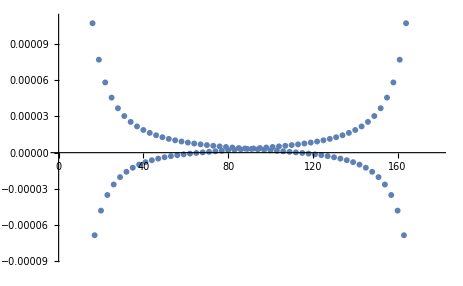

```mathematica
Show[ListPlot[ValueG1203]]
```